```mathematica
(* Here I am plotting the leading term of the "inner-regime" potential (without the perturbation) .... *)
```

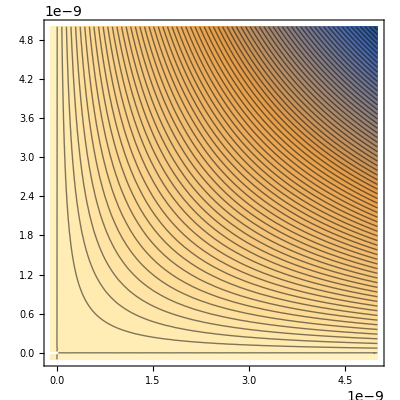

```mathematica
With[
{ϵ=0.001,λ=10^(-9),ϵ0=8.85*10^(-12),R=10^(-7),M=10},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}],{x,-ϵ R,0.05R},{y,-ϵ R,0.05R},Contours->70]
]
```

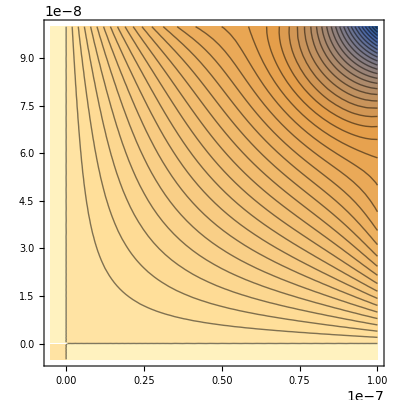

```mathematica
With[
{ϵ=10^(-4),λ=10^(-9),ϵ0=8.85*10^(-12),R=10^(-7),M=10},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+λ/(2π ϵ0)Log[R/Sqrt[x^2+y^2+2R^2-2 R(x+y)]]+λ Log[2]/(4π ϵ0),{x,-0.05R,R},{y,-0.05R,R},Contours->40]
]
```

```mathematica
(* Here I am seeing the characteristics of the equipotential lines ... As the slider of the Manipulate command proceeds the value of the potential approaches zero exponentially ... *)
```

```mathematica
Manipulate[
With[
{ϵ=10^(-4),λ=-10^(-9),ϵ0=8.85*10^(-12),R=10^(-7),M=10},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+λ/(2π ϵ0)Log[R/Sqrt[x^2+y^2+2R^2-2 R(x+y)]]+λ Log[2]/(4π ϵ0)==10^(n),{x,0,R},{y,0,R},ContourLabels->None]
],{n,4,-1}]
```

```mathematica
(* Some minor Maclaurin series for n tending to infinity .... *)
```

```mathematica
Series[(Cos[m θ]+βm Sin[m θ])/.{θ->R ϵr/n/r},{n,Infinity,1}]
```

1+(m R βm ϵr)/(r n)+O[1/n]^2

```mathematica
Series[((Cos[θ]+Sin[θ])^m-Cos[m θ]-Tan[m π/(4+2ϵ)] Sin[m θ])/.{θ->R ϵr/n/r},{n,Infinity,1}]
```

(m R ϵr-m R ϵr Tan[(m π)/(4+2 ϵ)])/(r n)+O[1/n]^2

```mathematica
Series[(Cos[m θ]+βm Sin[m θ])/.{θ->π/2-R ϵr/n/r},{n,Infinity,1}]
```

(Cos[(m π)/2]+βm Sin[(m π)/2])+(-m R βm ϵr Cos[(m π)/2]+m R ϵr Sin[(m π)/2])/(r n)+O[1/n]^2

```mathematica
Series[((Cos[θ]+Sin[θ])^m-Cos[m θ]-Tan[m π/(4+2ϵ)] Sin[m θ])/.{θ->π/2-R ϵr/n/r},{n,Infinity,1}]
```

(1-Cos[(m π)/2]-Sin[(m π)/2] Tan[(m π)/(4+2 ϵ)])+(m R ϵr-m R ϵr Sin[(m π)/2]+m R ϵr Cos[(m π)/2] Tan[(m π)/(4+2 ϵ)])/(r n)+O[1/n]^2

```mathematica
FullSimplify[Limit[(1-Cos[(m π)/2]-Sin[(m π)/2] Tan[(m π)/(4+2 ϵ)]),ϵ->0]]
```

0

```mathematica
FullSimplify[Limit[(1-Sin[(m π)/2]+Cos[(m π)/2] Tan[(m π)/(4+2 ϵ)]),ϵ->0]]
```

1-Tan[(m π)/4]

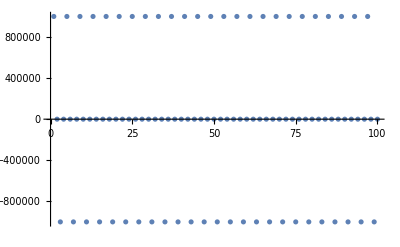

```mathematica
With[{β=10^(-6)},ListPlot[Table[Csc[m π/2+ArcTan[1/β]],{m,1,100,1}]]]
```

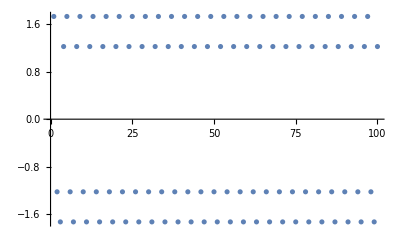

```mathematica
With[{β=1/Sqrt[2]},ListPlot[Table[Csc[m π/2+ArcTan[1/β]],{m,1,100,1}]]]
```

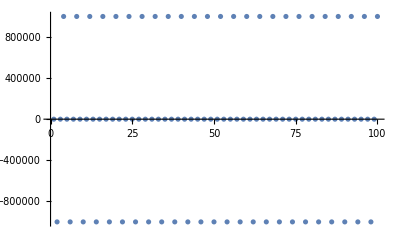

```mathematica
With[{β=10^(6)},ListPlot[Table[Csc[m π/2+ArcTan[1/β]],{m,1,100,1}]]]
```

```mathematica
FullSimplify[TrigExpand[Sin[m π/2+ArcTan[1/β]]],Assumptions->β>0]
```

(Cos[(m π)/2]+β Sin[(m π)/2])/(√(1+β^2))

```mathematica
Series[(Sin[m θ+ArcTan[β]])/.{θ->π/2-R ϵr/n/r},{n,Infinity,1}]
```

Sin[(m π)/2+ArcTan[β]]-(m R ϵr Cos[(m π)/2+ArcTan[β]])/(r n)+O[1/n]^2

```mathematica
(* Here I am plotting the matched asymptotic expansion of the potential for 0≤x<R/Sqrt[2] and 0≤y<R/Sqrt[2] (1/Sqrt[2] is approximately 0.71) .... *)
```

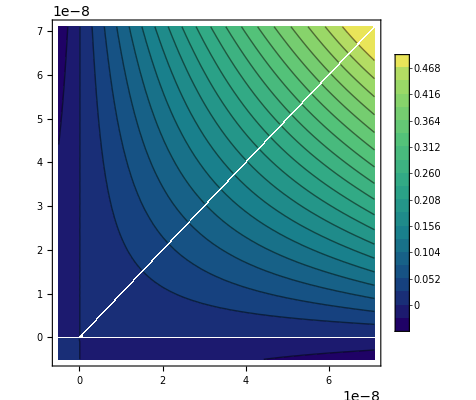

```mathematica
With[
{β=1/Sqrt[5],ϵ=10^(-3),λ=-10^(-13),ϵ0=8.85*10^(-12),R=10^(-7),n=10^10,M=11},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+λ/(2π ϵ0)Log[R/Sqrt[x^2+y^2+2R^2-2 R(x+y)]]+λ Log[2]/(4π ϵ0)+
If[
0≤ArcTan[x,y]<π/4,
1/n(1-Sqrt[x^2+y^2]/R)^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1) π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-λ Log[2]/(2Sqrt[2]π ϵ0 n) Sum[(Sqrt[x^2+y^2]/R)^m 1/(m+1)(2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Sin[m ArcTan[x,y]+ArcTan[β]]/Sin[m π/2+ArcTan[β]](1-Sin[(m+1)π/2]+Cos[(m+1)π/2]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}]
]
]
,{x,-0.05R,0.71R},{y,-0.05R,0.71R},Contours->20,ColorFunction->"BlueGreenYellow",ContourLabels->{None,Automatic},PlotLegends->Automatic]
]
```

```mathematica
(* Here I am plotting the matched asymptotic expansion of the potential for r->0 (a really small span from the corner); you can see that at least seemingly the equipotential lines squeeze in closer and closer to the corner .... *)
```

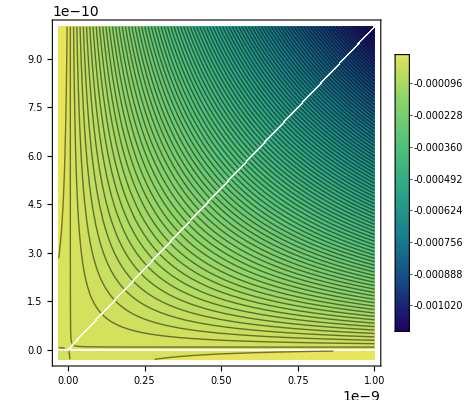

```mathematica
With[
{β=RandomReal[]*10,ϵ=10^(-4),λ=10^(-13),ϵ0=8.85*10^(-12),R=10^(-7),n=10^7,M=10},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+λ/(2π ϵ0)Log[R/Sqrt[x^2+y^2+2R^2-2 R(x+y)]]+λ Log[2]/(4π ϵ0)+
If[
0<ArcTan[x,y]<π/4,
1/n(1-Sqrt[x^2+y^2]/R)^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1) π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-λ Log[2]/(2Sqrt[2]π ϵ0 n) Sum[(Sqrt[x^2+y^2]/R)^m 1/(m+1)(2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Sin[(m ArcTan[x,y]+ArcTan[β])/(m π/2+ArcTan[β])](1-Sin[(m+1)π/2]+Cos[(m+1)π/2]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}]
]
]
,{x,-3*10^(-4)R,0.01R},{y,-3*10^(-4)R,0.01R},Contours->95,ColorFunction->"BlueGreenYellow",ContourLabels->{None,Automatic},PlotLegends->Automatic]
]
```

```mathematica
(* Here I am plotting the matched asymptotic expansion of the potential for x->R, y->R(a really small span from the linear charged thread); the potential lines are circular for a certain range and beyond that there are deformations ....  *)
```

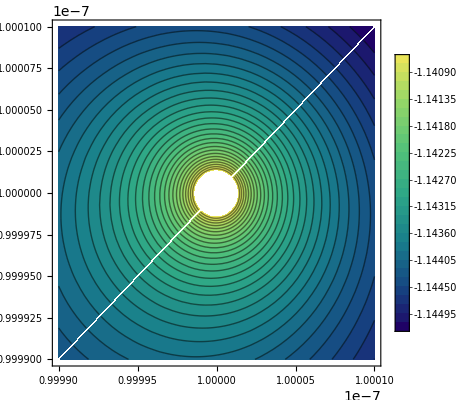

```mathematica
With[
{ϵ=10^(-3),ϵ1=10^(-4),λ=10^(-13),ϵ0=8.85*10^(-12),R=10^(-7),n=10^10,M=10},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+λ/(2π ϵ0)Log[R/Sqrt[x^2+y^2+2R^2-2 R(x+y)]]+λ Log[2]/(4π ϵ0)+
If[
0≤ArcTan[x,y]<π/4,
1/n(Abs[1-Sqrt[x^2+y^2]/R])^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1) π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-λ Log[2]/(2Sqrt[2]π ϵ0 n) Sum[(Sqrt[x^2+y^2]/R)^m 1/(m+1)(2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}],
1/n(Abs[1-Sqrt[x^2+y^2]/R])^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Sin[m ArcTan[x,y]+ArcTan[RandomReal[{0.01,100}]]]/Sin[m π/2+ArcTan[RandomReal[{0.01,100}]]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}]
]
]
,{x,R(1-ϵ1),R(1+ϵ1)},{y,R(1-ϵ1),R(1+ϵ1)},Contours->30,ColorFunction->"BlueGreenYellow",ContourLabels->{None,Automatic},PlotLegends->Automatic]
]
```

```mathematica
(* Here I am plotting the matched asymptotic expansion of the potential for the middle zone R/2 ≤ x ≤ R  *)
```

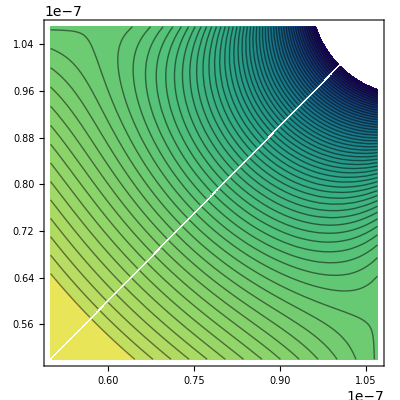

```mathematica
With[
{β=RandomReal[]*10,ϵ=10^(-4),λ=10^(-13),ϵ0=8.85*10^(-12),R=10^(-7),n=10^7,M=10},
ContourPlot[λ/(4π ϵ0)Sum[1/m(Sqrt[x^2+y^2]/R)^m (((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]- Tan[m π/(4+2ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+λ/(2π ϵ0)Log[R/Sqrt[x^2+y^2+2R^2-2 R(x+y)]]+λ Log[2]/(4π ϵ0)+
If[
0<ArcTan[x,y]<π/4,
1/n(1-Sqrt[x^2+y^2]/R)^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1) π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-λ Log[2]/(2Sqrt[2]π ϵ0 n) Sum[(Sqrt[x^2+y^2]/R)^m 1/(m+1)(2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n λ/(4π ϵ0) Sum[(Sqrt[x^2+y^2]/R)^m Sin[(m ArcTan[x,y]+ArcTan[β])/(m π/2+ArcTan[β])](1-Sin[(m+1)π/2]+Cos[(m+1)π/2]Tan[(m+1)π/(4+2ϵ)]),{m,1,M}]
]
]
,{x,0.5R,1.07R},{y,0.5R,1.07R},Contours->63,ColorFunction->"BlueGreenYellow",ContourLabels->{None,Automatic}]
]
```

```mathematica
(* Here I am plotting a sample from what one obtains from the finite element method; the field lines progress well in terms of the order,but the shapes do not seem to agree, I may want to be a little experimental on this in the future ......  *)
```

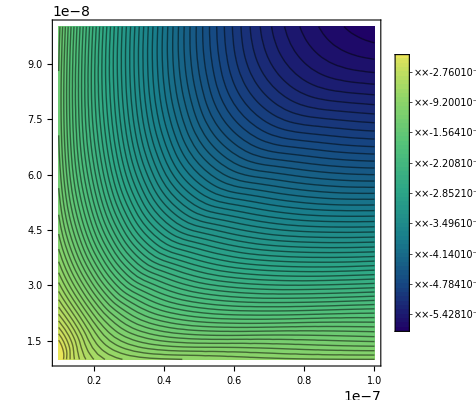

```mathematica
Block[
{potent,f,ϵ,δ,ϵ0,R,λ,ϕ0,r,θ},
δ=10^(-6);ϵ=10^(-6);λ=10^(-13);ϵ0=8.85*10^(-12);R=10^(-7);
potent=NDSolveValue[{Laplacian[f[r,θ],{r,θ},"Polar"]==(-λ Sqrt[2]R)/(2π ϵ0 r)  DiracDelta[r-Sqrt[2]R]DiracDelta[θ-π/4],f[r,0]==δ,f[r,π/(2+ϵ)]==δ},f[r,θ],{r,0,2R},{θ,0,π/(2+ϵ)}];
ContourPlot[(potent-δ)/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},{x,0.1R,R},{y,0.1R,R},Contours->63,ColorFunction->"BlueGreenYellow",ContourLabels->{None,Automatic},PlotLegends->Automatic]
]
```